```mathematica
pascal[m_]:=Table[Table[{n,k,Binomial[n,k]},{k,0,n}],{n,0,m}]
barva[n_]:=Gray/;Mod[n,2]==1
barva[n_]:=White/;Mod[n,2]==0
pascalCtverecky[seznam_]:=Map[{barva[#[[3]]],EdgeForm[Black],Rectangle[{#[[2]]-#[[1]]/2,-#[[1]]},{#[[2]]-#[[1]]/2+1,-#[[1]]+1}]}&,seznam]
```

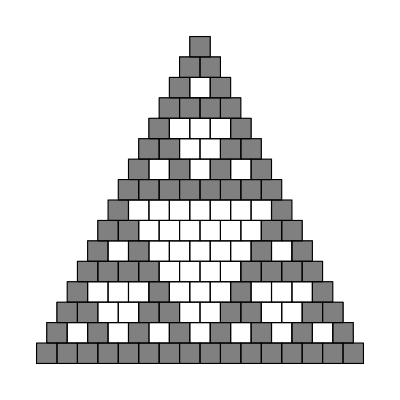

```mathematica
Graphics[pascalCtverecky[Flatten[pascal[15],1]]]
```

```mathematica
"Pouze lichá kombinační čísla jsou v řádcích, které jsou mocninami dvojky (když je číslujeme od 1)"
```

```mathematica
uhelAn[n_]:=Sum[ArcTan[1/Sqrt[i]],{i,1,n-1}]
```

```mathematica
polomerAn[n_]:=Sqrt[n]
```

```mathematica
zPolDoKart[polomer_,uhel_]:={polomer*Cos[uhel],polomer*Sin[uhel]}
```

```mathematica
vrcholyAn[n_]:=Table[zPolDoKart[polomerAn[i],uhelAn[i]],{i,1,n}]
```

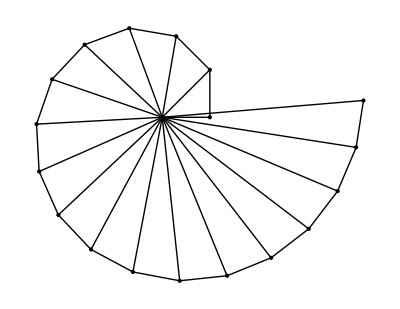

```mathematica
vrcholy=vrcholyAn[18];

Graphics[{Point[{0,0}],Map[Point,vrcholy],Map[Line,Table[vrcholy[[i;;i+1]],{i,1,Length[vrcholy]-1}]],Map[Line,Table[{{0,0},vrcholy[[i]]},{i,1,Length[vrcholy]}]]}]
```

```mathematica
"Je potřeba 17 trojúhelníků"
```

```mathematica
stredy[s_]:=
RotateLeft[1/2*{{s[[1,1]]+s[[2,1]],s[[1,2]]+s[[2,2]]},{s[[2,1]]+s[[3,1]],s[[2,2]]+s[[3,2]]},{s[[3,1]]+s[[1,1]],s[[3,2]]+s[[1,2]]}},1]
```

```mathematica
stredy[{{1,1},{1,2},{2,1}}]
```

{{3/2,3/2},{3/2,1},{1,3/2}}

```mathematica
teziste[s_]:=Map[1/3*#&,MapThread[Plus,s]]
```

```mathematica
teziste[{{1,1},{1,2},{2,1}}]
```

{4/3,4/3}

```mathematica
paty[s_]:={s[[2]]+Projection[s[[1]]-s[[2]],s[[3]]-s[[2]]],s[[3]]+Projection[s[[2]]-s[[3]],s[[1]]-s[[3]]],s[[1]]+Projection[s[[3]]-s[[1]],s[[2]]-s[[1]]]}
```

```mathematica
paty[{{1,1},{1,2},{2,1}}]
```

{{3/2,3/2},{1,1},{1,1}}

```mathematica
Clear[ortocentrum]
ortocentrum[s_]:=Flatten[Solve[(y-s[[1,2]]) (paty[s][[1,1]]-s[[1,1]])==(x-s[[1,1]]) (paty[s][[1,2]]-s[[1,2]])&&(y-s[[2,2]]) (paty[s][[2,1]]-s[[2,1]])==(x-s[[2,1]]) (paty[s][[2,2]]-s[[2,2]]),{x,y}]]
```

```mathematica
ortocentrum[{{1,1},{2,1},{1,2}}]
```

{x→1,y→1}

```mathematica
vykresliTrojuhelnik[s_]:=Graphics[{{Line[{s[[1]],s[[2]],s[[3]],s[[1]]}]},{Orange,PointSize[0.02],Point[stredy[s]]},{Dashed,Line[{s[[1]],stredy[s][[1]]}],Line[{s[[2]],stredy[s][[2]]}],Line[{s[[3]],stredy[s][[3]]}]},{Blue,PointSize[0.02],Point[teziste[s]]},{Red,PointSize[0.02],Point[paty[s]]},{DotDashed,Line[{s[[1]],paty[s][[1]]}],Line[{s[[2]],paty[s][[2]]}],Line[{s[[3]],paty[s][[3]]}]},{Green,PointSize[0.02],Point[{x,y}/.ortocentrum[s]]}},PlotRangePadding->0.5,Axes->True]
```

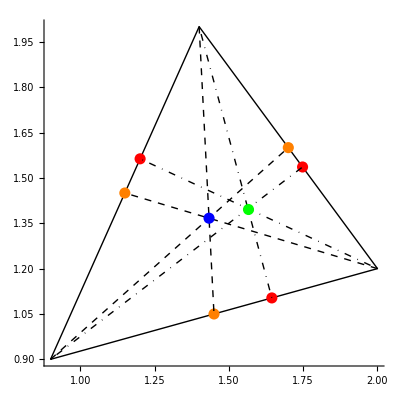

```mathematica
vykresliTrojuhelnik[{{0.9,0.9},{2,1.2},{1.4,2}}]
```